# Celoštevilsko linearno programiranje

## Neceloštevilski podatki

Celoštevilska naloga s podatki

```mathematica
m={{21.7,-18.2,-19.4}}
b={{2.3,0}}
c={1,1,1}
```

{{21.7,-18.2,-19.4}}

{{2.3,0}}

{1,1,1}

```mathematica
LinearProgramming[c,m,b,Automatic,Integers]
```

{1,0,1}

je ekvivalentna nalogi

```mathematica
m={{7,-2,-4,-10}}
b={{3,0}}
c={1,1,1,0}
```

{{7,-2,-4,-10}}

{{3,0}}

{1,1,1,0}

```mathematica
LinearProgramming[c,m,b,Automatic,Integers]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{1,0,1,0}

## Razveji in razdeli

### Prvi primer

```mathematica
m={{1,2,3},{3,5,6}};
b={4,11};
c={0,1,0};
```

```mathematica
LinearProgramming[c,m,Partition[Riffle[b,Table[0,{Length[b]}]],2]]
```

{3,0,1/3}

```mathematica
(m1=Join[m,{{0,0,1}}])//MatrixForm
```

(1 | 2 | 3
3 | 5 | 6
0 | 0 | 1)

```mathematica
b1a ={{4,0},{11,0},{0,-1}}
LinearProgramming[c,m1,b1a]
```

{{4,0},{11,0},{0,-1}}

{2,1,0}

```mathematica
b1b ={{4,0},{11,0},{1,1}}
LinearProgramming[c,m1,b1b]
```

{{4,0},{11,0},{1,1}}

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{0,1,0},{{1,2,3},{3,5,6},{0,0,1}},{{4,0},{11,0},{1,1}}]

Rešitev smo dobili že v enem koraku. Preverimo, da je rešitev prava.

```mathematica
LinearProgramming[c,m,Partition[Riffle[b,Table[0,{Length[b]}]],2],Automatic,Integers]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{2,1,0}

### Drugi primer

#### Podatki

```mathematica
SeedRandom[1234]
```

```mathematica
m=3;n=4;
```

```mathematica
(a = Table[RandomInteger[{1,10}],{m},{n}])//MatrixForm
```

(1 | 7 | 10 | 7
1 | 8 | 1 | 1
9 | 5 | 5 | 9)

```mathematica
x = {0,1,1,2}
```

{0,1,1,2}

```mathematica
b = a.x
```

{31,11,28}

```mathematica
c= {1,1,-1,0}
```

{1,1,-1,0}

```mathematica
ilp=LinearProgramming[c,a,Partition[Riffle[b,Table[0,{Length[b]}]],2],Automatic,Integers]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{0,1,1,2}

#### Prvi korak razveji in razdeli na prvo spremenljivko

```mathematica
LinearProgramming[c,N[a],Partition[Riffle[b,Table[0,{Length[b]}]],2]]
```

{1.30807,0.920923,2.32455,0.}

```mathematica
(a1=Join[a,{{1,0,0,0}}])//MatrixForm
```

(1 | 7 | 10 | 7
1 | 8 | 1 | 1
9 | 5 | 5 | 9
1 | 0 | 0 | 0)

WolframAlphaQueryResults

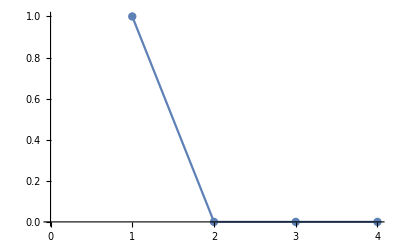

Rešitev se izraža v obliki seznama.

```mathematica
b1a = Join[Partition[Riffle[b,Table[0,{Length[b]}]],2],{{1,-1}}]
ilp1a=LinearProgramming[c,N[a1],b1a]
```

{{31,0},{11,0},{28,0},{1,-1}}

{1.,0.939547,2.01259,0.471033}

Tukaj ni rešitve, zato prepiše ukaz LinearProgramming.

```mathematica
b1b = Join[Partition[Riffle[b,Table[0,{Length[b]}]],2],{{2,1}}]
ilp1b=LinearProgramming[c,a1,b1b]
```

{{31,0},{11,0},{28,0},{2,1}}

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{1,1,-1,0},{{1,7,10,7},{1,8,1,1},{9,5,5,9},{1,0,0,0}},{{31,0},{11,0},{28,0},{2,1}}]

```mathematica
LinearProgramming[{1,1,-1,0},{{1,7,10,7},{1,8,1,1},{9,5,5,9},{1,0,0,0}},{{31,0},{11,0},{28,0},{2,1}}]
```

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{1,1,-1,0},{{1,7,10,7},{1,8,1,1},{9,5,5,9},{1,0,0,0}},{{31,0},{11,0},{28,0},{2,1}}]

#### Drugi korak razveji in razdeli na drugo spremenljivko

```mathematica
(a2=Join[a1,{{0,1,0,0}}])//MatrixForm
```

(1 | 7 | 10 | 7
1 | 8 | 1 | 1
9 | 5 | 5 | 9
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

Pogojujemo na drugo spremenljivko, zato dodamo vrstico 0 1 0 0.

(1 | 7 | 10 | 7
1 | 8 | 1 | 1
9 | 5 | 5 | 9
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
b2a = Join[b1a,{{0,-1}}]
ilp2a=LinearProgramming[c,N[a2],b2a]
```

{{31,0},{11,0},{28,0},{1,-1},{0,-1}}

LinearProgramming::lpsnf: No solution can be found that satisfies the constraints.

LinearProgramming[{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1.,0.,0.,0.},{0.,1.,0.,0.}},{{31,0},{11,0},{28,0},{1,-1},{0,-1}}]

```mathematica
b2b = Join[b1a,{{1,1}}]
ilp2b=LinearProgramming[c,N[a2],b2b]
```

{{31,0},{11,0},{28,0},{1,-1},{1,1}}

{3.44343×10^-16,1.,1.,2.}

## Ukaz razveji in razdeli

Chop zaokroži z natačnostjo plavajoče vejice. Position dobi mesto.

```mathematica
NajdiPrvoNecelostevilcnoKomponento[lst_]:= Module[{pom},pom=Position[Chop[lst-Floor[lst]],_Real];If[Length[pom]>0,First[pom],{}]]
```

```mathematica
NajdiPrvoNecelostevilcnoKomponento[{1.02,1.,-0.123}]
```

{1}

```mathematica
NajdiPrvoNecelostevilcnoKomponento[{2.,-1.02,1.,-0.123}]
```

{2}

```mathematica
NajdiPrvoNecelostevilcnoKomponento[{1,2,3,4}]
```

{}

```mathematica
c = {1, 1, -1, 0};
b = {{31,0},{11,0},{28,0}};
a={{1,7,10,7},{1,8,1,1},{9,5,5,9}};
a=N[a]; (*za računanje večjih problemov, da je hitrejše*)
```

```mathematica
KorakRazvejiInRazdeli[c_,a_,b_]:= Module[{n,lp,i,i1,lb,ub,a0,a1,bl,bu,lpl,lpu,jj,il,iu},
n = Length[c];
lp = LinearProgramming[c,a,b];
i=NajdiPrvoNecelostevilcnoKomponento[N[lp]];
If[Length[i]>0,
(i1= i[[1]];
lb = Floor[lp[[i1]]];
ub = lb +1;
a0 = ReplacePart[Table[0,{n}],i1-> 1]; (* razširimo matriko z dodatno vrstico; same ničle, razen na mesto nove vezi, to je na i1, damo enko *)
a1 = Join[a,{a0}];
bl=Join[b,{{lb,-1}}]; (* možnost a, to je spodnja meja *)
bu=Join[b,{{ub,1}}]; (* možnost b, to je zgornja meja *)
lpl = Quiet[LinearProgramming[c,a1,bl]]; (* Quiet ne javlja opozorila, če naloga nima rešitve *)
lpu = Quiet[LinearProgramming[c,a1,bu]];
jj=Position[{Head[lpl]== List,Head[lpu]== List},True]; (* Ugotovimo, katera veja je rešitev (vrne seznam) *)
If[Length[jj]==2,
(il=NajdiPrvoNecelostevilcnoKomponento[N[lpl]];
iu=NajdiPrvoNecelostevilcnoKomponento[N[lpu]];
If[Length[il]== 0,CelostevilcnaResitev[lpl],CelostevilcnaResitev[lpu]]),
If[jj=={{1}},{c,a1,bl},{c,a1,bu}]]),
CelostevilcnaResitev[lp]]]
```

```mathematica
b0 = Partition[Riffle[b,Table[0,{3}]],2]
```

{{31,0},{11,0},{28,0}}

```mathematica
a = {{1,7,10,7},{1,8,1,1},{9,5,5,9}};
```

```mathematica
c = {1,1,-1,0};
```

```mathematica
pom=KorakRazvejiInRazdeli[c,a,b]
```

{{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1,0,0,0}},{{31,0},{11,0},{28,0},{1,-1}}}

```mathematica
pom1=Apply[KorakRazvejiInRazdeli,pom]
```

{{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1,0,0,0},{0,1,0,0}},{{31,0},{11,0},{28,0},{1,-1},{1,1}}}

```mathematica
pom2=Apply[KorakRazvejiInRazdeli,pom1]
```

{{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1,0,0,0},{0,1,0,0},{0,0,0,1}},{{31,0},{11,0},{28,0},{1,-1},{1,1},{2,1}}}

```mathematica
pom3=Apply[KorakRazvejiInRazdeli,pom2]
```

{{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1,0,0,0},{0,1,0,0},{0,0,0,1},{1,0,0,0}},{{31,0},{11,0},{28,0},{1,-1},{1,1},{2,1},{0,1}}}

```mathematica
pom4=Apply[KorakRazvejiInRazdeli,pom3]
```

{{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1,0,0,0},{0,1,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,0}},{{31,0},{11,0},{28,0},{1,-1},{1,1},{2,1},{0,1},{0,1}}}

```mathematica
pom5 = Apply[KorakRazvejiInRazdeli,pom4]
```

{{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1,0,0,0},{0,1,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{31,0},{11,0},{28,0},{1,-1},{1,1},{2,1},{0,1},{0,1},{0,1}}}

```mathematica
flag = True;
lpdata = {c,a,b};
i = 0; nmax = 5;
While[flag,i++;lpdata = Apply[KorakRazvejiInRazdeli,lpdata];flag = i ≤ nmax && Length[lpdata]>1]
lpdata
```

{{1,1,-1,0},{{1.,7.,10.,7.},{1.,8.,1.,1.},{9.,5.,5.,9.},{1,0,0,0},{0,1,0,0},{0,0,0,1},{1,0,0,0},{1,0,0,0},{1,0,0,0}},{{31,0},{11,0},{28,0},{1,-1},{1,1},{2,1},{0,1},{0,1},{0,1}}}

### Še en primer

#### Podatki

```mathematica
SeedRandom[1234]
```

```mathematica
m=8;n=10;
```

```mathematica
(a = Table[RandomInteger[{1,10}],{m},{n}])//MatrixForm
```

(1 | 7 | 10 | 7 | 1 | 8 | 1 | 1 | 9 | 5
5 | 9 | 6 | 10 | 8 | 3 | 9 | 5 | 6 | 9
7 | 2 | 7 | 2 | 3 | 1 | 4 | 7 | 7 | 1
8 | 5 | 4 | 8 | 10 | 7 | 7 | 1 | 3 | 3)

```mathematica
x = Table[RandomInteger[{0,2}],{n}]
```

{2,1,1,2,0,1,0,1,1,1}

```mathematica
b = a.x
```

{56,68,43,55,44,38,87,71}

```mathematica
b0=Partition[Riffle[b,Table[0,{Length[b]}]],2]
```

{{56,0},{68,0},{43,0},{55,0},{44,0},{38,0},{87,0},{71,0}}

```mathematica
c= Table[RandomInteger[{-1,1}],{n}]
```

{-1,1,0,-1,-1,1,1,-1,1,-1}

```mathematica
ilp=LinearProgramming[c,a,b0,Automatic,Integers]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{2,1,1,2,0,1,0,1,1,1}

```mathematica
flag = True;
lpdata = {c,a,b0};
i = 0; nmax = 100; (* Omejimo število iteracij *)
While[flag,i++;lpdata = Apply[KorakRazvejiInRazdeli,lpdata];flag = i ≤ nmax && Length[lpdata]>1]
lpdata
```

CelostevilcnaResitev[{2,1,1,2,0,1,0,1,1,1}]

#### Podatki

```mathematica
SeedRandom[1234]
```

```mathematica
m=4;n=10;
```

```mathematica
(a = Table[RandomInteger[{1,10}],{m},{n}])//MatrixForm
```

(1 | 7 | 10 | 7 | 1 | 8 | 1 | 1 | 9 | 5
5 | 9 | 6 | 10 | 8 | 3 | 9 | 5 | 6 | 9
7 | 2 | 7 | 2 | 3 | 1 | 4 | 7 | 7 | 1
8 | 5 | 4 | 8 | 10 | 7 | 7 | 1 | 3 | 3)

```mathematica
x = Table[RandomInteger[{0,2}],{n}]
```

{0,2,0,1,0,0,1,1,0,0}

```mathematica
b = a.x
```

{23,42,17,26}

```mathematica
b0=Partition[Riffle[b,Table[0,{Length[b]}]],2]
```

{{23,0},{42,0},{17,0},{26,0}}

```mathematica
c= Table[RandomInteger[{-1,1}],{n}]
```

{1,-1,0,-1,1,0,0,1,-1,0}

```mathematica
ilp=LinearProgramming[c,a,b0,Automatic,Integers]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

{0,2,0,1,0,0,1,1,0,0}

```mathematica
flag = True;
lpdata = {c,a,b0};
i = 0; nmax = 100;
While[flag,i++;lpdata = Apply[KorakRazvejiInRazdeli,lpdata];flag = i ≤ nmax && Length[lpdata]>1]
lpdata
```

CelostevilcnaResitev[{0,2,0,1,0,0,1,1,0,0}]